```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

## Ze plot data

#### Orbit 1607

```mathematica
time={"01:03:50.199","01:03:50.830","01:03:51.461","01:03:52.092","01:03:52.723","01:03:53.354","01:03:53.985","01:03:54.616","01:03:55.248","01:03:55.879","01:03:56.510","01:03:57.141","01:03:57.772","01:03:58.403","01:03:59.034","01:03:59.665","01:04:00.296","01:04:00.927","01:04:01.558","01:04:02.189","01:04:02.820","01:04:03.451","01:04:04.083","01:04:04.714","01:04:05.345","01:04:05.976","01:04:06.607","01:04:07.238","01:04:07.869","01:04:08.500","01:04:09.131","01:04:09.762","01:04:10.393","01:04:11.024","01:04:11.656","01:04:12.287","01:04:12.918","01:04:13.549","01:04:14.180","01:04:14.811","01:04:15.442","01:04:16.073","01:04:16.704","01:04:17.335","01:04:17.966","01:04:18.597","01:04:19.229","01:04:19.860","01:04:20.491","01:04:21.122","01:04:21.753","01:04:22.384","01:04:23.015","01:04:23.646","01:04:24.277","01:04:24.908","01:04:25.539","01:04:26.171","01:04:26.802","01:04:27.433","01:04:28.064","01:04:28.695","01:04:29.326","01:04:29.957","01:04:30.588","01:04:31.219","01:04:31.850","01:04:32.481","01:04:33.113","01:04:33.744","01:04:34.375","01:04:35.006","01:04:35.637","01:04:36.268","01:04:36.899","01:04:37.530","01:04:38.161","01:04:38.792","01:04:39.424","01:04:40.055","01:04:40.686","01:04:41.317","01:04:41.948","01:04:42.579","01:04:43.210","01:04:43.841","01:04:44.472","01:04:45.103","01:04:45.735","01:04:46.366","01:04:46.997","01:04:47.628","01:04:48.259","01:04:48.890","01:04:49.521","01:04:50.152","01:04:50.783","01:04:51.414","01:04:52.046","01:04:52.677","01:04:53.308","01:04:53.939","01:04:54.570","01:04:55.201","01:04:55.832","01:04:56.463","01:04:57.094","01:04:57.725","01:04:58.357","01:04:58.988","01:04:59.619","01:05:00.250","01:05:00.881","01:05:01.512","01:05:02.143","01:05:02.774","01:05:03.405","01:05:04.037","01:05:04.668","01:05:05.299","01:05:05.930","01:05:06.561","01:05:07.192","01:05:07.823","01:05:08.454","01:05:09.085","01:05:09.717","01:05:10.348","01:05:10.979","01:05:11.610","01:05:12.241","01:05:12.872","01:05:13.503","01:05:14.134","01:05:14.766","01:05:15.397","01:05:16.028","01:05:16.659","01:05:17.290","01:05:17.921","01:05:18.552","01:05:19.183","01:05:19.814","01:05:20.446","01:05:21.077","01:05:21.708","01:05:22.339","01:05:22.970","01:05:23.601","01:05:24.232","01:05:24.863","01:05:25.495","01:05:26.126","01:05:26.757","01:05:27.388","01:05:28.019","01:05:28.650","01:05:29.281","01:05:29.912","01:05:30.544","01:05:31.175","01:05:31.806","01:05:32.437","01:05:33.068","01:05:33.699","01:05:34.330","01:05:34.961","01:05:35.593","01:05:36.224","01:05:36.855","01:05:37.486","01:05:38.117","01:05:38.748","01:05:39.379","01:05:40.010","01:05:40.642","01:05:41.273","01:05:41.904","01:05:42.535","01:05:43.166","01:05:43.797","01:05:44.428","01:05:45.059","01:05:45.691","01:05:46.322","01:05:46.953","01:05:47.584","01:05:48.215","01:05:48.846","01:05:49.477","01:05:50.109","01:05:50.740","01:05:51.371","01:05:52.002","01:05:52.633","01:05:53.264","01:05:53.895","01:05:54.527","01:05:55.158","01:05:55.789","01:05:56.420","01:05:57.051","01:05:57.682","01:05:58.313","01:05:58.944","01:05:59.576","01:06:00.207","01:06:00.838","01:06:01.469","01:06:02.100","01:06:02.731","01:06:03.362","01:06:03.994","01:06:04.625"}; pots={101.92,117.60,117.60,101.92,235.20,282.24,344.96,344.96,282.24,101.92,101.92,101.92,117.60,172.48,141.12,141.12,172.48,172.48,117.60,141.12,172.48,172.48,101.92,101.92,203.84,203.84,282.24,203.84,282.24,344.96,344.96,282.24,203.84,203.84,141.12,117.60,141.12,235.20,235.20,282.24,282.24,235.20,203.84,141.12,117.60,101.92,101.92,101.92,141.12,101.92,101.92,117.60,141.12,141.12,141.12,141.12,101.92,101.92,101.92,141.12,141.12,141.12,141.12,117.60,141.12,101.92,117.60,172.48,172.48,203.84,282.24,235.20,203.84,203.84,235.20,282.24,282.24,282.24,344.96,407.68,282.24,282.24,407.68,407.68,407.68,282.24,282.24,407.68,407.68,407.68,344.96,282.24,470.40,470.40,407.68,344.96,172.48,101.92,203.84,172.48,101.92,203.84,203.84,344.96,282.24,235.20,235.20,172.48,172.48,172.48,172.48,203.84,203.84,203.84,172.48,172.48,141.12,172.48,172.48,141.12,141.12,172.48,172.48,172.48,203.84,235.20,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,344.96,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,235.20,203.84,203.84,172.48,172.48,172.48,172.48,172.48,141.12,117.60,117.60,172.48,172.48,203.84,172.48,141.12,141.12,141.12,141.12,172.48,172.48,203.84,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,203.84,235.20,203.84,172.48,172.48,141.12,141.12,141.12,117.60,117.60,101.92,101.92,101.92,117.60,117.60,117.60,117.60,117.60,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,101.92,117.60,117.60,101.92,101.92,101.92,101.92,101.92,101.92,101.92}; curs={0.154,0.112,0.123,0.387,0.838,0.949,1.082,1.086,0.860,0.244,0.131,0.161,0.525,0.603,0.460,0.537,0.554,0.652,0.475,0.552,0.689,0.654,0.389,0.717,1.260,0.776,1.552,1.104,1.397,1.447,1.129,1.059,0.734,0.759,0.492,0.403,0.406,0.568,1.024,1.247,1.170,0.863,0.699,0.556,0.457,0.348,0.061,0.100,0.434,0.220,0.656,0.441,0.411,0.863,0.808,0.744,0.324,0.242,0.347,0.607,0.646,0.763,0.721,0.670,0.580,0.309,0.613,0.885,0.794,1.026,1.305,0.991,0.914,0.965,1.256,1.476,1.529,1.125,1.768,2.266,1.356,1.314,2.481,2.244,1.978,1.189,1.099,1.776,2.359,2.121,1.727,1.492,2.425,2.366,1.795,1.622,0.920,0.216,0.747,0.732,0.171,0.794,1.770,1.851,1.699,1.311,1.597,1.616,1.459,1.278,1.056,1.166,1.352,1.068,0.774,0.789,0.582,0.680,0.580,0.518,0.497,0.762,0.661,0.705,0.823,0.980,1.306,1.457,1.522,1.349,1.363,1.376,1.414,1.211,1.492,1.738,2.090,1.673,1.969,1.747,1.772,1.720,1.590,1.649,1.731,1.452,1.283,1.081,0.995,0.829,0.859,1.018,0.728,0.837,0.596,0.572,0.970,1.084,1.551,1.017,1.066,1.092,1.277,0.970,1.380,1.485,1.811,1.458,1.581,1.869,1.611,1.317,1.574,1.584,1.503,1.503,1.798,1.680,1.386,1.205,0.968,0.632,0.636,0.632,0.568,0.267,0.190,0.298,0.574,0.690,0.720,0.671,0.528,0.231,0.127,0.106,0.138,0.166,0.165,0.131,0.241,0.194,0.112,0.107,0.078,0.069,0.071,0.054,0.105,0.237,0.516,0.230,0.189,0.158};
curErrs={0.020,0.017,0.018,0.021,0.033,0.041,0.050,0.042,0.039,0.028,0.014,0.016,0.029,0.036,0.031,0.026,0.027,0.037,0.029,0.030,0.033,0.041,0.028,0.026,0.040,0.045,0.055,0.060,0.054,0.070,0.060,0.059,0.040,0.049,0.044,0.035,0.038,0.048,0.052,0.057,0.064,0.062,0.053,0.046,0.030,0.043,0.024,0.016,0.024,0.044,0.041,0.044,0.035,0.032,0.030,0.028,0.021,0.021,0.022,0.028,0.025,0.027,0.025,0.026,0.025,0.032,0.027,0.034,0.026,0.034,0.041,0.035,0.031,0.040,0.039,0.045,0.040,0.031,0.039,0.044,0.032,0.036,0.056,0.051,0.047,0.043,0.040,0.052,0.056,0.064,0.060,0.057,0.062,0.070,0.056,0.056,0.029,0.033,0.041,0.037,0.025,0.033,0.043,0.051,0.048,0.046,0.051,0.047,0.039,0.060,0.048,0.052,0.053,0.060,0.048,0.051,0.035,0.045,0.040,0.039,0.035,0.057,0.050,0.057,0.052,0.050,0.063,0.055,0.056,0.061,0.057,0.059,0.058,0.070,0.081,0.082,0.085,0.090,0.104,0.094,0.078,0.100,0.096,0.079,0.079,0.074,0.095,0.073,0.063,0.052,0.056,0.053,0.043,0.053,0.043,0.043,0.050,0.079,0.086,0.077,0.059,0.082,0.085,0.092,0.080,0.115,0.109,0.085,0.087,0.151,0.119,0.105,0.127,0.178,0.150,0.122,0.128,0.164,0.141,0.211,0.232,0.027,0.026,0.027,0.026,0.024,0.019,0.021,0.024,0.032,0.034,0.029,0.028,0.020,0.016,0.017,0.014,0.021,0.019,0.016,0.021,0.022,0.014,0.022,0.012,0.019,0.031,0.027,0.025,0.026,0.031,0.032,0.016,0.018};
jes={0.050,0.041,0.055,0.113,0.227,0.311,0.380,0.358,0.250,0.077,0.045,0.048,0.119,0.146,0.109,0.121,0.125,0.149,0.094,0.119,0.149,0.156,0.099,0.153,0.305,0.184,0.422,0.288,0.416,0.452,0.344,0.310,0.178,0.179,0.108,0.082,0.085,0.138,0.281,0.368,0.347,0.224,0.172,0.118,0.099,0.078,0.021,0.031,0.098,0.063,0.139,0.103,0.102,0.195,0.190,0.156,0.101,0.085,0.100,0.168,0.172,0.209,0.185,0.168,0.163,0.106,0.144,0.234,0.210,0.307,0.396,0.278,0.257,0.256,0.369,0.450,0.495,0.357,0.619,0.852,0.436,0.431,1.069,0.951,0.826,0.413,0.376,0.721,0.999,0.797,0.611,0.492,1.024,1.009,0.699,0.580,0.269,0.082,0.216,0.229,0.086,0.222,0.471,0.596,0.555,0.389,0.419,0.345,0.299,0.283,0.248,0.310,0.355,0.285,0.205,0.214,0.157,0.178,0.148,0.154,0.133,0.217,0.179,0.205,0.241,0.308,0.436,0.495,0.503,0.438,0.435,0.442,0.475,0.408,0.505,0.552,0.697,0.541,0.645,0.562,0.565,0.548,0.534,0.539,0.542,0.425,0.350,0.276,0.259,0.202,0.234,0.272,0.199,0.217,0.149,0.138,0.235,0.257,0.370,0.240,0.230,0.229,0.266,0.226,0.295,0.325,0.419,0.297,0.369,0.419,0.352,0.303,0.388,0.424,0.388,0.386,0.458,0.411,0.324,0.286,0.217,0.145,0.140,0.144,0.133,0.084,0.063,0.078,0.126,0.158,0.156,0.137,0.117,0.067,0.053,0.050,0.055,0.067,0.091,0.065,0.088,0.079,0.060,0.060,0.052,0.060,0.046,0.039,0.054,0.081,0.125,0.071,0.062,0.058};
jeErrs={0.100,0.030,0.051,0.042,0.077,0.108,0.059,0.053,0.055,0.060,0.024,0.030,0.177,0.078,0.050,0.042,0.049,0.123,0.074,0.055,0.044,0.081,0.060,0.060,0.066,0.082,0.058,0.054,0.062,0.099,0.077,0.069,0.042,0.045,0.049,0.044,0.090,0.081,0.066,0.069,0.075,0.073,0.060,0.061,1.371,0.199,0.244,34.469,0.081,0.035,0.060,0.043,0.045,0.055,0.163,0.042,0.118,0.035,0.039,0.054,0.066,0.055,0.046,0.043,0.048,0.043,0.038,0.052,0.092,0.064,0.099,0.050,0.111,0.050,0.063,0.067,0.068,0.102,0.063,0.063,0.054,0.079,0.106,0.083,0.081,0.063,0.070,0.084,0.096,0.091,0.084,0.083,0.100,0.103,0.081,0.084,0.060,0.033,0.066,0.063,0.027,0.056,0.058,0.078,0.076,0.076,0.074,0.052,0.048,0.068,0.049,0.079,0.059,0.069,0.070,0.085,0.066,0.072,0.044,0.080,0.038,0.083,0.055,0.074,0.067,0.065,0.103,0.091,0.089,0.100,0.078,0.080,0.084,0.106,0.112,0.102,0.118,0.115,0.138,0.117,0.122,0.126,0.117,0.109,0.099,0.083,0.102,0.077,0.074,0.054,0.072,0.098,0.114,0.066,0.058,0.053,0.078,0.078,0.162,0.071,0.064,0.156,0.122,0.114,0.146,0.153,0.113,0.090,0.114,0.127,0.108,0.105,0.177,3.788,0.590,0.274,0.424,0.213,0.247,0.251,4.130,0.043,0.039,0.504,0.071,0.028,0.053,0.053,0.327,0.049,0.053,0.032,0.053,0.063,0.031,0.027,0.060,0.066,0.096,0.045,0.087,0.073,0.039,0.059,0.021,0.027,0.032,0.059,0.034,0.031,0.046,0.027,0.029,0.190};
```

### Orbit 1607

```mathematica
(*time={"09:00:01.220","09:00:02.484","09:00:03.748","09:00:05.011","09:00:06.275","09:00:07.539","09:00:08.802","09:00:10.066","09:00:11.330","09:00:12.593","09:00:13.857","09:00:15.121","09:00:16.384","09:00:17.648","09:00:18.912","09:00:20.176","09:00:21.439","09:00:22.703","09:00:23.967","09:00:25.230","09:00:26.494","09:00:27.758","09:00:29.021","09:00:30.285","09:00:31.549","09:00:32.813","09:00:34.076","09:00:35.340","09:00:36.604","09:00:37.867","09:00:39.131","09:00:40.395","09:00:41.659","09:00:42.922","09:00:44.186","09:00:45.450","09:00:46.714","09:00:47.977","09:00:49.241","09:00:50.505","09:00:51.769","09:00:53.032","09:00:54.296","09:00:55.560","09:00:56.823","09:00:58.087","09:00:59.351","09:01:00.615","09:01:01.879","09:01:03.142","09:01:04.406","09:01:05.670","09:01:06.934","09:01:08.197","09:01:09.461","09:01:10.725","09:01:11.989","09:01:13.253","09:01:14.516","09:01:15.780","09:01:17.044","09:01:18.308","09:01:19.571","09:01:20.835","09:01:22.099","09:01:23.363","09:01:24.627","09:01:25.890","09:01:27.154","09:01:28.418","09:01:29.682","09:01:30.946","09:01:32.209","09:01:33.473","09:01:34.737","09:01:36.001","09:01:37.265","09:01:38.528","09:01:39.792","09:01:41.056","09:01:42.320","09:01:43.584","09:01:44.848","09:01:46.111","09:01:47.375","09:01:48.639","09:01:49.903","09:01:51.167","09:01:52.431","09:01:53.694","09:01:54.958","09:01:56.222","09:01:57.486","09:01:58.750","09:02:00.014","09:02:01.277","09:02:02.541","09:02:03.805","09:02:05.069","09:02:06.333","09:02:07.597","09:02:08.861","09:02:10.125","09:02:11.388","09:02:12.652","09:02:13.916","09:02:15.180","09:02:16.444","09:02:17.708","09:02:18.972","09:02:20.236","09:02:21.499","09:02:22.763","09:02:24.027","09:02:25.291","09:02:26.555","09:02:27.819","09:02:29.083","09:02:30.347","09:02:31.611","09:02:32.874","09:02:34.138","09:02:35.402","09:02:36.666","09:02:37.930","09:02:39.194","09:02:40.458","09:02:41.722","09:02:42.986","09:02:44.250","09:02:45.514","09:02:46.778","09:02:48.041","09:02:49.305","09:02:50.569","09:02:51.833","09:02:53.097","09:02:54.361","09:02:55.625","09:02:56.889","09:02:58.153","09:02:59.417","09:03:00.681","09:03:01.945","09:03:03.209","09:03:04.473","09:03:05.737","09:03:07.001","09:03:08.265","09:03:09.528","09:03:10.792","09:03:12.056","09:03:13.320","09:03:14.584","09:03:15.848","09:03:17.112","09:03:18.376","09:03:19.640","09:03:20.904","09:03:22.168","09:03:23.432","09:03:24.696","09:03:25.960","09:03:27.224","09:03:28.488","09:03:29.752","09:03:31.016","09:03:32.280","09:03:33.544","09:03:34.808","09:03:36.072","09:03:37.336","09:03:38.600","09:03:39.864","09:03:41.128","09:03:42.392","09:03:43.656","09:03:44.920","09:03:46.184","09:03:47.448","09:03:48.712","09:03:49.976","09:03:51.240","09:03:52.504","09:03:53.768","09:03:55.032","09:03:56.296","09:03:57.560","09:03:58.824","09:04:00.088","09:04:01.352","09:04:02.616","09:04:03.880","09:04:05.144","09:04:06.408","09:04:07.673","09:04:08.937","09:04:10.201","09:04:11.465","09:04:12.729","09:04:13.993","09:04:15.257","09:04:16.521","09:04:17.785","09:04:19.049","09:04:20.313","09:04:21.577","09:04:22.841","09:04:24.105","09:04:25.369","09:04:26.633","09:04:27.897","09:04:29.162","09:04:30.426","09:04:31.374","09:04:32.638"};
pots={470.40,815.36,1128.96,1379.84,1128.96,1128.96,940.80,1128.96,940.80,940.80,940.80,1128.96,940.80,940.80,1128.96,940.80,940.80,940.80,940.80,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,940.80,1128.96,1379.84,1630.72,1630.72,1630.72,1881.60,1630.72,1630.72,1630.72,1630.72,1379.84,1379.84,1630.72,1379.84,1379.84,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1379.84,1379.84,1630.72,1881.60,2257.92,2759.68,2759.68,3261.44,3261.44,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,5519.36,5519.36,5519.36,4515.84,4515.84,4515.84,3763.20,3261.44,3261.44,2759.68,2759.68,2257.92,2257.92,2257.92,1881.60,1379.84,1128.96,940.80,940.80,689.92,815.36,1128.96,1128.96,1128.96,1128.96,1379.84,1379.84,1128.96,1128.96,1379.84,1630.72,1630.72,1881.60,1881.60,1881.60,1881.60,1128.96,1379.84,1379.84,1379.84,1379.84,1630.72,1881.60,2257.92,2257.92,2257.92,2257.92,1881.60,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2759.68,2759.68,2759.68,2759.68,2759.68,2759.68,2257.92,2257.92,2257.92,3261.44,3261.44,3763.20,3763.20,3763.20,3763.20,3763.20,4515.84,4515.84,4515.84,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,5519.36,4515.84,4515.84,4515.84,4515.84,3763.20,3763.20,4515.84,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,4515.84,4515.84,5519.36,4515.84,1379.84,344.96,470.40,564.48,689.92,815.36,940.80,940.80,815.36,1128.96,1128.96,1128.96,1630.72,1630.72,1379.84,1379.84,1379.84,1128.96,1379.84,1379.84,1128.96,940.80,689.92,564.48,470.40,470.40,407.68,407.68,407.68,470.40,470.40,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,407.68,689.92,470.40,564.48,470.40,470.40};
curs={0.210,0.244,0.271,0.309,0.464,0.504,0.392,0.469,0.512,0.446,0.529,0.619,0.473,0.476,0.344,0.358,0.298,0.261,0.278,0.298,0.332,0.352,0.395,0.448,0.381,0.332,0.295,0.282,0.375,0.413,0.516,0.561,0.665,0.501,0.406,0.290,0.310,0.337,0.336,0.285,0.330,0.347,0.344,0.359,0.356,0.321,0.222,0.235,0.203,0.282,0.417,0.509,0.558,0.626,0.486,0.380,0.487,0.414,0.346,0.355,0.369,0.400,0.555,0.746,0.808,0.752,0.850,0.707,0.508,0.537,0.524,0.604,0.731,0.710,0.922,0.806,0.616,0.582,0.468,0.426,0.384,0.351,0.273,0.283,0.231,0.218,0.171,0.233,0.436,0.605,0.610,0.466,0.493,0.418,0.348,0.385,0.390,0.535,0.571,0.569,0.642,0.751,0.616,0.572,0.526,0.392,0.323,0.351,0.402,0.301,0.311,0.335,0.406,0.409,0.465,0.454,0.483,0.444,0.476,0.495,0.449,0.436,0.498,0.655,0.641,0.642,0.575,0.606,0.639,0.484,0.366,0.365,0.647,0.648,0.641,0.672,0.712,0.627,0.476,0.476,0.517,0.529,0.509,0.524,0.537,0.603,0.623,0.681,0.638,0.633,0.438,0.399,0.384,0.384,0.426,0.338,0.301,0.287,0.389,0.423,0.414,0.430,0.450,0.493,0.659,1.313,2.899,4.011,4.639,4.331,0.014,0.522,0.446,0.479,0.371,0.518,0.511,0.375,0.455,0.603,0.624,0.828,0.931,0.617,0.610,0.617,0.515,0.618,0.938,0.845,0.670,0.433,0.364,0.305,0.249,0.213,0.258,0.235,0.323,0.224,0.059,0.129,0.095,0.100,0.037,0.032,0.027,0.013,0.007,0.003,0.001,0.002,0.001,0.002,0.004,0.005};
curErrs={0.021,0.023,0.012,0.011,0.015,0.015,0.013,0.014,0.017,0.015,0.016,0.016,0.016,0.016,0.017,0.014,0.017,0.015,0.015,0.014,0.019,0.019,0.019,0.020,0.025,0.020,0.017,0.016,0.022,0.026,0.029,0.028,0.031,0.028,0.027,0.023,0.023,0.024,0.025,0.021,0.029,0.031,0.031,0.029,0.036,0.030,0.030,0.024,0.024,0.024,0.036,0.037,0.040,0.039,0.049,0.044,0.055,0.062,0.065,0.053,0.087,0.078,0.102,0.087,0.173,0.180,0.036,0.030,0.027,0.028,0.026,0.027,0.037,0.035,0.044,0.037,0.032,0.029,0.024,0.023,0.023,0.022,0.010,0.010,0.010,0.009,0.008,0.013,0.016,0.018,0.022,0.023,0.025,0.021,0.015,0.019,0.018,0.020,0.021,0.021,0.023,0.022,0.017,0.019,0.016,0.014,0.017,0.015,0.017,0.017,0.017,0.023,0.022,0.021,0.023,0.024,0.024,0.020,0.019,0.025,0.026,0.024,0.025,0.034,0.033,0.034,0.037,0.031,0.038,0.032,0.036,0.026,0.045,0.045,0.049,0.055,0.053,0.048,0.036,0.045,0.054,0.044,0.060,0.065,0.073,0.070,0.060,0.054,0.088,0.084,0.076,0.072,0.063,0.087,0.110,0.090,0.104,0.152,0.020,0.021,0.023,0.026,0.026,0.026,0.031,0.050,0.075,0.087,0.090,0.037,0.003,0.018,0.025,0.027,0.011,0.013,0.015,0.013,0.014,0.016,0.018,0.020,0.041,0.032,0.042,0.037,0.017,0.017,0.020,0.021,0.019,0.016,0.015,0.015,0.013,0.013,0.014,0.013,0.016,0.012,0.007,0.010,0.010,0.011,0.006,0.005,0.004,0.004,0.003,0.009,0.002,0.009,0.000,0.001,0.051,0.004};
jes={0.553,0.474,0.456,0.528,0.666,0.719,0.594,0.699,0.783,0.703,0.778,0.901,0.706,0.737,0.646,0.623,0.574,0.540,0.648,0.692,0.730,0.782,0.800,0.781,0.723,0.689,0.579,0.487,0.634,0.680,0.847,1.014,1.175,0.977,0.973,0.687,0.691,0.736,0.681,0.567,0.620,0.665,0.709,0.734,0.656,0.499,0.398,0.389,0.369,0.423,0.559,0.707,0.853,1.076,1.072,1.040,1.361,1.307,1.218,1.332,1.311,1.435,2.056,2.803,3.032,2.914,3.431,3.047,2.255,2.493,2.474,2.761,3.055,2.838,3.465,2.842,2.014,1.823,1.400,1.153,0.949,0.850,0.663,0.605,0.424,0.338,0.250,0.264,0.312,0.495,0.602,0.509,0.536,0.451,0.414,0.451,0.438,0.588,0.702,0.782,0.853,1.086,0.904,0.851,0.749,0.496,0.457,0.494,0.524,0.476,0.501,0.595,0.807,0.756,0.817,0.738,0.738,0.711,0.780,0.861,0.836,0.839,1.003,1.325,1.309,1.376,1.324,1.431,1.566,1.157,0.839,0.847,1.839,1.798,1.986,2.058,2.245,2.058,1.691,1.782,2.019,2.249,2.421,2.567,2.511,2.652,2.656,2.933,2.800,2.888,2.107,1.916,1.730,1.631,1.748,1.321,1.104,1.045,1.455,1.543,1.436,1.469,1.574,1.744,2.325,4.809,10.694,15.626,14.939,5.786,0.020,0.360,0.292,0.391,0.354,0.534,0.560,0.372,0.526,0.767,0.803,1.246,1.502,0.858,0.847,0.840,0.682,0.814,1.222,0.956,0.684,0.345,0.268,0.220,0.184,0.154,0.182,0.173,0.242,0.162,0.059,0.116,0.105,0.098,0.046,0.034,0.028,0.016,0.008,0.007,0.004,0.007,0.002,0.006,0.010,0.006};
jeErrs={0.192,0.125,0.095,0.123,0.132,0.193,0.095,0.098,0.104,0.109,0.125,0.122,0.098,0.122,0.098,0.092,0.107,0.099,0.099,0.101,0.121,0.115,0.123,0.107,0.120,0.112,0.088,0.105,0.113,0.138,0.158,0.161,0.184,0.169,0.179,0.138,0.130,0.147,0.137,0.105,0.148,0.162,0.168,0.176,0.392,0.254,2.066,0.166,0.130,0.101,0.378,0.152,0.147,0.170,0.239,0.658,0.378,0.544,0.467,0.692,0.688,0.555,4.323,0.693,5.254,7.833,0.324,0.332,0.295,0.282,0.273,0.294,0.349,0.297,0.366,0.306,0.271,0.237,0.193,0.167,0.171,0.179,0.077,0.071,0.062,0.070,0.057,0.060,0.083,0.081,0.110,0.104,0.120,0.100,0.071,0.077,0.078,0.113,0.093,0.073,0.089,0.141,0.086,0.074,0.085,0.137,0.093,0.075,0.077,0.084,0.083,0.119,0.101,0.087,0.086,0.084,0.087,0.078,0.085,0.096,0.128,0.134,0.136,0.172,0.159,0.194,0.210,0.176,0.230,0.221,0.287,0.197,0.305,0.343,0.328,0.413,0.354,0.361,0.276,0.362,0.616,0.389,0.603,0.583,0.677,0.592,0.477,0.470,0.888,0.696,1.045,0.742,0.642,0.713,0.907,1.024,2.317,1.531,0.189,0.201,0.209,0.241,0.221,0.242,0.268,0.458,0.624,0.786,0.642,0.161,0.154,0.135,0.227,0.104,0.089,0.095,0.091,0.087,0.098,0.123,0.112,0.136,0.230,0.174,0.263,0.207,0.100,0.097,0.113,0.099,0.102,0.078,0.077,0.113,0.069,0.077,0.057,0.099,0.073,0.051,0.052,0.043,0.060,0.051,0.026,1.314,0.035,0.044,0.017,0.015,0.013,-NaN,0.006,0.687,0.288,0.008};*)
```

### Data for first and second portions of arc in which we are interested

```mathematica
inds1=Range[78,110];
inds2=Range[119,174];
inds3={3,4}~Join~inds2;
```

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

### Lil plot to check out J-V relation on the fly

```mathematica
ind1Start=74;ind1End=90;ind1Init=78;ind2Init=110;
```

```mathematica
ind1Start=110;ind1End=139;ind1Init=119;ind2Init=174;
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{200,Max[pots]},{0,Max[curs]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Lil plot to check out energy flux–voltage relation on the fly

```mathematica
ind1Start=74;ind1End=90;ind1Init=78;ind2Init=113;
```

```mathematica
ind1Start=110;ind1End=139;ind1Init=119;ind2Init=174;
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]},{0,Max[jes]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

J-V fits

## Nonlinear fits for first portion of arc

### Now the actual fits

```mathematica
kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<100000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<100000};
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[plotData1,{kModel,kConstraints},{{kFitN,1},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->plotDataWts1]
```

FittedModel[2093.53 (1-0.99999/((1+1.18645×10^-6 pot)^0.584285))]

```mathematica
gFit=NonlinearModelFit[plotData1,{gModel,gConstraints},{{gFitN,1},{gFitT,300},{gFitRB,10}},pot,Weights->plotDataWts1]
```

FittedModel[13780.2 (1-0.99999 ⅇ^(-1.00002×10^-7 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts1]/kDOF}
```

{0.169496,100.001,99999.9,1.58428,52.4259}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts1]/gDOF}
```

{0.516142,100.,99998.9,52.008}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.169496 | 39336.6 | 4.30887×10^-6 | 0.999997
kFitT | 100.001 | 7.93868×10^8 | 1.25967×10^-7 | 1.
kFitRB | 99999.9 | 8.43591×10^10 | 1.18541×10^-6 | 0.999999
kFitKappa | 1.58428 | 781901. | 2.0262×10^-6 | 0.999998

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.516142 | 0.949067 | 0.543842 | 0.590569
gFitT | 100. | 470.07 | 0.212734 | 0.832973
gFitRB | 99998.9 | 2.79535×10^8 | 0.000357733 | 0.999717

### Ze plot

```mathematica
plotData1[[;;,1]]
```

{1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,940.8,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1128.96,940.8,1128.96,1128.96,1128.96,940.8,940.8,1128.96,1881.6,2257.92,1881.6,2257.92,2257.92,2257.92,2257.92,2759.68,2759.68,2759.68,3261.44}

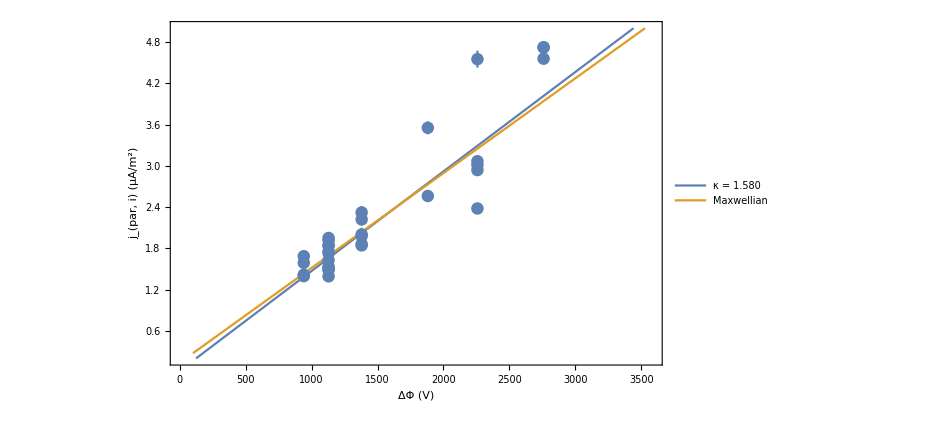

```mathematica
Show[Plot[{kFit[pot],gFit[pot]},{pot,100,10000},PlotRange->{{0,Max[plotData1[[;;,1]]]*11/10},{0.2,5}},PlotLegends->((Style[#,20])&/@{StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]]
```

## Nonlinear fits for second portion of arc

### Now the actual fits

```mathematica
kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[plotData2,{kModel,kConstraints},{{kFitN,1},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->plotDataWts2]
```

FittedModel[32.9544 (1-0.999/(1+0.0000189996 pot)^1.02685)]

```mathematica
gFit=NonlinearModelFit[plotData2,{gModel,gConstraints},{{gFitN,1},{gFitT,300},{gFitRB,10}},pot,Weights->plotDataWts2]
```

FittedModel[60.7716 (1-0.999 ⅇ^(-0.00001001 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts2]/kDOF}
```

{0.153169,100.,999.999,2.02685,64.0413}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts2]/gDOF}
```

{0.227621,100.,999.998,62.6737}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.153169 | 55.8589 | 0.00274208 | 0.997823
kFitT | 100. | 308806. | 0.000323828 | 0.999743
kFitRB | 999.999 | 1.56973×10^6 | 0.00063705 | 0.999494
kFitKappa | 2.02685 | 3348.16 | 0.000605363 | 0.999519

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {gFitN, 0.22762063587153794, 0.15972885755558222, 1.4250439110060675, 0.16000705892709144}, {gFitT, 100.00001798377369, 204.31773587826078, 0.4894338592483082, 0.6265541771816758}, {gFitRB, 999.9978745279175, 26382.65996011885, 0.037903603201479945, 0.9699069518816414}}
```

### Ze plot

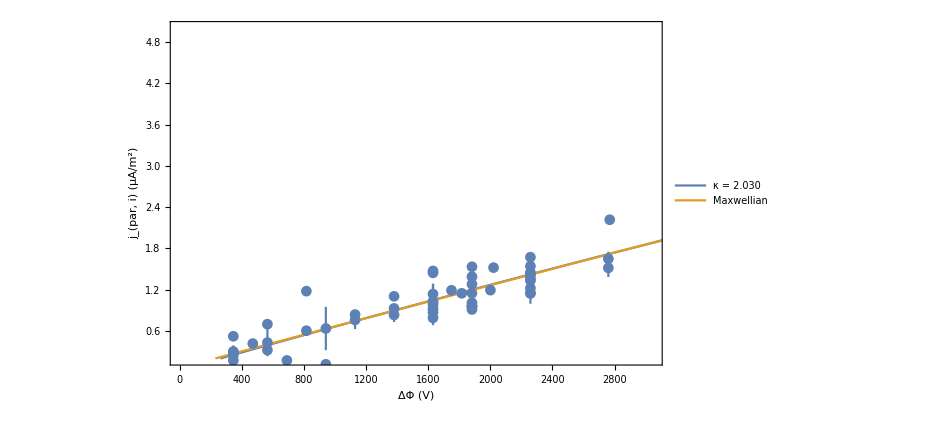

```mathematica
Show[Plot[{kFit[pot],gFit[pot]},{pot,100,10000},PlotRange->{{0,Max[plotData2[[;;,1]]]*11/10},{0.2,5}},PlotLegends->((Style[#,20])&/@{StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]]
```

## Linear model for second half of arc

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

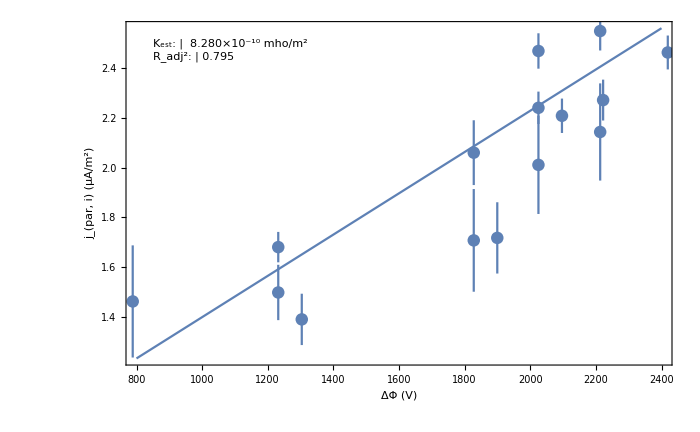

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

### Assess it

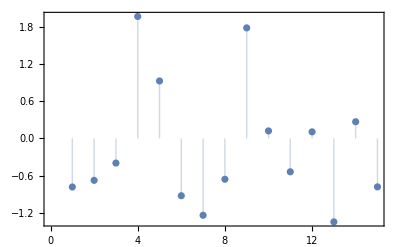

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

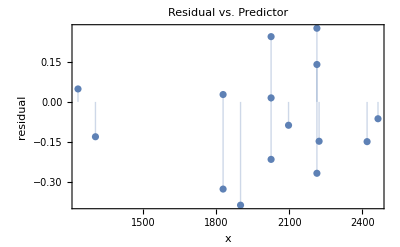

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

## Artificially combine parts of each

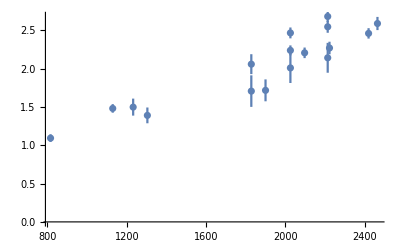

```mathematica
ErrorListPlot[errorData3]
```

## Simultaneously fit both sets of data, allowing RB to be different for each

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDat = Join[plotData1/.{x_,y_}->{1,x,y},plotData2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=plotDataWts1~Join~plotDataWts2;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gCombFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kCombConstraints={1<kFitRB1<5000,1<kFitRB2<5000,50<kFitT<5000,0.1<kFitN<10,1.51<kFitKappa<35};
gCombConstraints={1<gFitRB1<5000,1<gFitRB2<5000,50<gFitT<5000,0.1<gFitN<10};
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB1,3},{kFitRB2,10},{kFitT,300},{kFitN,1},{kFitKappa,5}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,(0.0266987 «5»)/((1-1/(«19»)) «1» Gamma[«1»]),set==2,(0.0266987 0.178864 «19» √(«1») (1-(1-1/107.164) (1+«1»)^(1-«19»)) Gamma[1+1.51])/((1-1/1.51) 1.51^(3/2) Gamma[-1/2+1.51])]]

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gCombConstraints},{{gFitRB1,3},{gFitRB2,10},{gFitT,300},{gFitN,1}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,0.0266987 0.364857 (1-ⅇ^(-pot/(«1»)) (1-1/(«18»))) 5000. √50.,set==2,0.0266987 0.364857 (1-ⅇ^(-pot/((-1+19.1135) «18»)) (1-1/19.1135)) 19.1135 √50.]]

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB1,kCombRB2,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF}
```

{5000.,107.164,840.445,0.178864,1.51,57.0021}

```mathematica
{gCombRB1,gCombRB2,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF}
```

{5000.,19.1135,50.,0.364857,64.0348}

```mathematica
RBinit1=gCombRB1;RBinit2=gCombRB2;Tminit=gCombT;nminit=gCombN;
```

### Mess ‘round

```mathematica
Manipulate[Row[{Manipulate[Show[Plot[{JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa1,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]],{{RB1,RBinit1},1.01,5000},{{kappa1,kappainit},1.501,35}],Manipulate[Show[Plot[{JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa2]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa2,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]],{{RB2,RBinit2},1.01,5000},{{kappa2,kappainit},1.501,35}]}],{{Tm,Tminit},3,500},{{nm,nminit},0.1,5}]
```

### Just tell ‘em, Hammer

```mathematica
combRepl={RB1->gCombRB1,RB2->gCombRB2,Tm->gCombT,nm->gCombN,kappa1->kCombKappa};
```

```mathematica
parNames={"T_m : ","n_m : ","R_B : "};
vals1=MapThread[NumberForm,{({Tm,nm,RB1}/.combRepl),{{3,0},{3,2},{3,1}}}];
vals2=MapThread[NumberForm,{({Tm,nm,RB2}/.combRepl),{{3,0},{3,2},{3,1}}}];
```

```mathematica
parTable1=Text[Grid[Transpose[{parNames,vals1}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
parTable2=Text[Grid[Transpose[{parNames,vals2}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
```

```mathematica
title1=StringJoin@Riffle[StringDrop[time[[inds1[[{1,-1}]]]],11],"–"]
title2=StringJoin@Riffle[StringDrop[time[[inds2[[{1,-1}]]]],11],"–"]
```

09:26:11.332–09:26:22.708

09:26:56.837–09:27:06.950

```mathematica
seg1Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,2.5}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 1 (`1`)",title1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]];
```

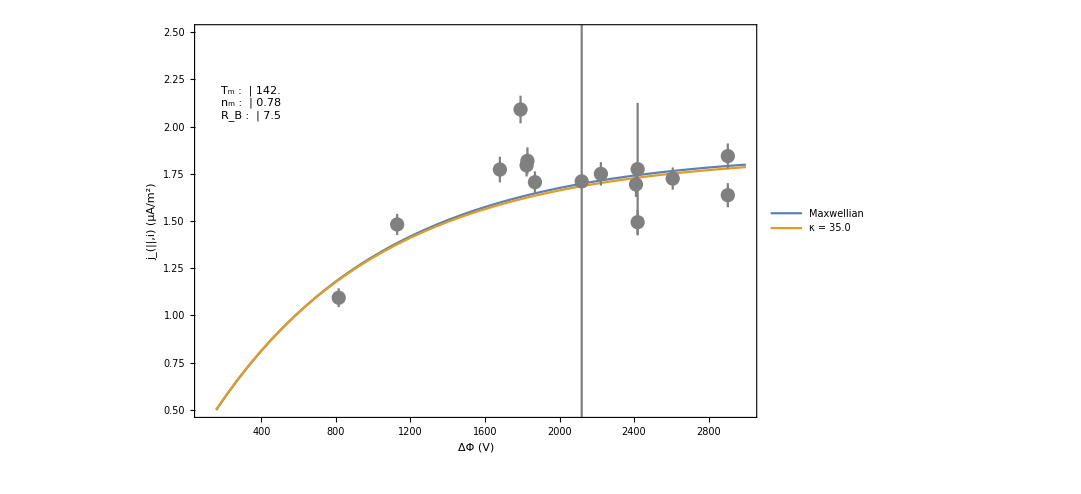

```mathematica
seg1Plot=Show[seg1Plotp1,ErrorListPlot[errorData1,PlotStyle->Gray]]
```

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

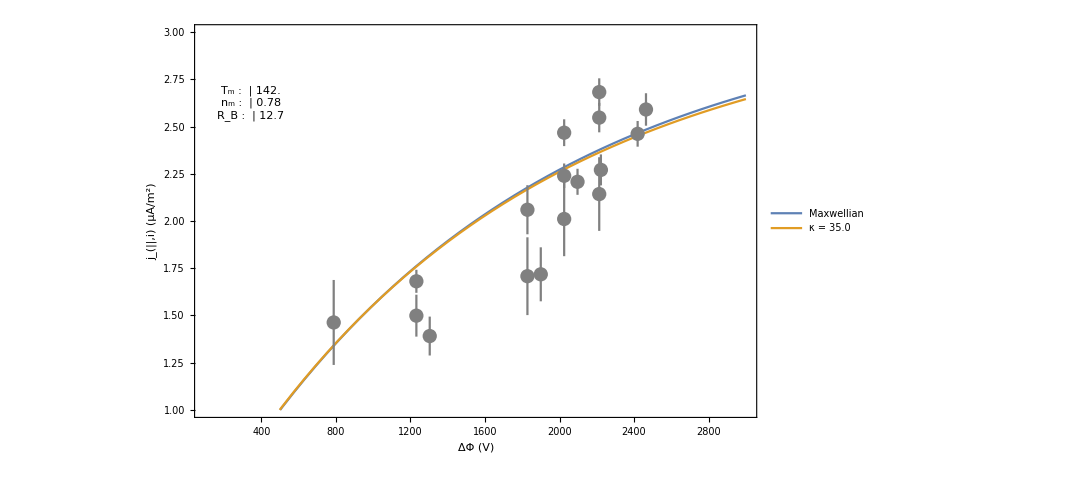

```mathematica
seg2Plot=Show[seg2Plotp1,ErrorListPlot[errorData2,PlotStyle->Gray]]
```

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

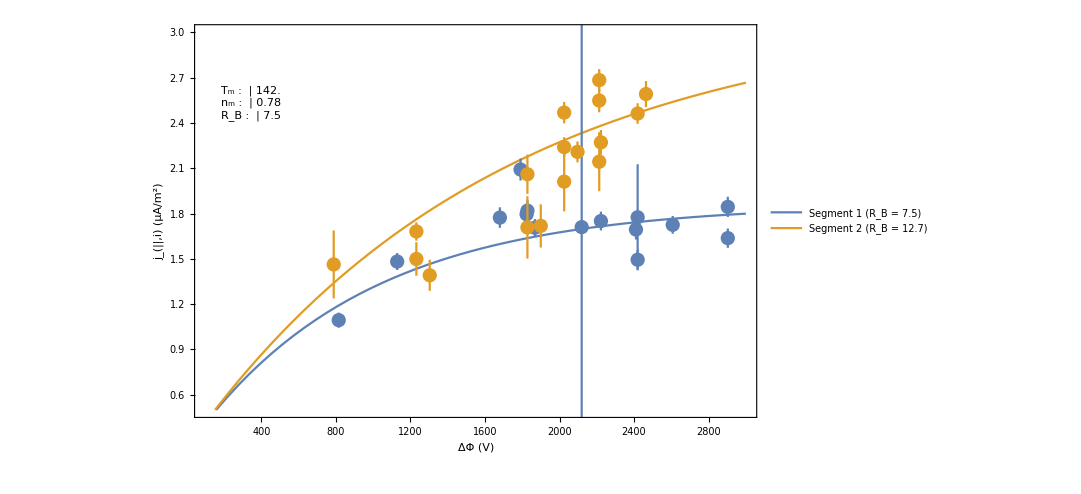

```mathematica
seg2Plot=Show[Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVMaxwellian[pot,RB2,Tm,nm]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,3}},PlotLegends->Map[(Style[#,23])&,MapThread[(StringForm["Segment `1` (R_B = `2`)",#1,NumberForm[#2,{3,1}]])&,({{"1","2"},{RB1,RB2}}/.combRepl)]],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style["Combined Segments",Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]],ErrorListPlot[{errorData1,errorData2}]]
```

J_E-V fits

## Nonlinear fits for first portion of arc

### Now the actual fits

```mathematica
kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<100000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<100000};
```

```mathematica
kModel = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jeData1,{kModel,kConstraints},{{kFitN,1},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->jeDataWts1]
```

FittedModel[190.129 (1-0.999/((1+7.8012×10^-6 pot)^1.78314))]

```mathematica
gFit=NonlinearModelFit[jeData1,{gModel,gConstraints},{{gFitN,1},{gFitT,300},{gFitRB,10}},pot,Weights->jeDataWts1]
```

FittedModel[257.069 (1-0.999 ⅇ^(-0.00001001 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts1]/kDOF}
```

{0.783318,100.,1000.,2.78314,1033.21}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts1]/gDOF}
```

{0.962852,100.,1000.,1005.44}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.783318 | 1369.41 | 0.000572012 | 0.999548
kFitT | 100. | 993091. | 0.000100696 | 0.99992
kFitRB | 1000. | 8.97918×10^6 | 0.000111369 | 0.999912
kFitKappa | 2.78314 | 45635.4 | 0.0000609864 | 0.999952

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.962852 | 4.0853 | 0.235687 | 0.815277
gFitT | 100. | 1090.19 | 0.0917273 | 0.927524
gFitRB | 1000. | 56450.7 | 0.0177146 | 0.985984

### Ze plot

```mathematica
plotData1[[;;,1]]
```

{1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,940.8,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1128.96,940.8,1128.96,1128.96,1128.96,940.8,940.8,1128.96,1881.6,2257.92,1881.6,2257.92,2257.92,2257.92,2257.92,2759.68,2759.68,2759.68,3261.44}

```mathematica
Show[Plot[{kFit[pot],gFit[pot]},{pot,100,10000},PlotRange->{{0,Max[plotData1[[;;,1]]]*11/10},{0.2,5}},PlotLegends->((Style[#,20])&/@{StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]]
```

```mathematica
t
```

## Nonlinear fits for second portion of arc

### Now the actual fits

```mathematica
kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[plotData2,{kModel,kConstraints},{{kFitN,1},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->plotDataWts2]
```

FittedModel[32.9544 (1-0.999/(1+0.0000189996 pot)^1.02685)]

```mathematica
gFit=NonlinearModelFit[plotData2,{gModel,gConstraints},{{gFitN,1},{gFitT,300},{gFitRB,10}},pot,Weights->plotDataWts2]
```

FittedModel[60.7716 (1-0.999 ⅇ^(-0.00001001 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts2]/kDOF}
```

{0.153169,100.,999.999,2.02685,64.0413}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts2]/gDOF}
```

{0.227621,100.,999.998,62.6737}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.153169 | 55.8589 | 0.00274208 | 0.997823
kFitT | 100. | 308806. | 0.000323828 | 0.999743
kFitRB | 999.999 | 1.56973×10^6 | 0.00063705 | 0.999494
kFitKappa | 2.02685 | 3348.16 | 0.000605363 | 0.999519

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {gFitN, 0.22762063587153794, 0.15972885755558222, 1.4250439110060675, 0.16000705892709144}, {gFitT, 100.00001798377369, 204.31773587826078, 0.4894338592483082, 0.6265541771816758}, {gFitRB, 999.9978745279175, 26382.65996011885, 0.037903603201479945, 0.9699069518816414}}
```

### Ze plot

```mathematica
Show[Plot[{kFit[pot],gFit[pot]},{pot,100,10000},PlotRange->{{0,Max[plotData2[[;;,1]]]*11/10},{0.2,5}},PlotLegends->((Style[#,20])&/@{StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]]
```

-Graphics-

## Linear model for second half of arc

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

-Graphics-

### Assess it

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

-Graphics-

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

-Graphics-

## Artificially combine parts of each

```mathematica
ErrorListPlot[errorData3]
```

-Graphics-

## Simultaneously fit both sets of data, allowing RB to be different for each

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDat = Join[plotData1/.{x_,y_}->{1,x,y},plotData2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=plotDataWts1~Join~plotDataWts2;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gCombFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kCombConstraints={1<kFitRB1<5000,1<kFitRB2<5000,50<kFitT<5000,0.1<kFitN<10,1.51<kFitKappa<35};
gCombConstraints={1<gFitRB1<5000,1<gFitRB2<5000,50<gFitT<5000,0.1<gFitN<10};
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB1,3},{kFitRB2,10},{kFitT,300},{kFitN,1},{kFitKappa,5}},{set,pot},Weights->combWts]
```

$Aborted

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gCombConstraints},{{gFitRB1,3},{gFitRB2,10},{gFitT,300},{gFitN,1}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,0.0266987 0.364857 (1-ⅇ^(-pot/(«1»)) (1-1/(«18»))) 5000. √50.,set==2,0.0266987 0.364857 (1-ⅇ^(-pot/((-1+19.1135) «18»)) (1-1/19.1135)) 19.1135 √50.]]

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB1,kCombRB2,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF}
```

{5000.,107.164,840.445,0.178864,1.51,57.0021}

```mathematica
{gCombRB1,gCombRB2,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF}
```

{5000.,19.1135,50.,0.364857,64.0348}

```mathematica
RBinit1=gCombRB1;RBinit2=gCombRB2;Tminit=gCombT;nminit=gCombN;
```

```mathematica
RBinit1=kCombRB1;RBinit2=kCombRB2;Tminit=kCombT;nminit=kCombN;kappainit=kCombN;
```

### Mess ‘round

```mathematica
Manipulate[Row[{Manipulate[Show[Plot[{JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa1,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]],{{RB1,RBinit1},1.01,5000},{{kappa1,kappainit},1.501,35}],Manipulate[Show[Plot[{JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa2]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa2,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]],{{RB2,RBinit2},1.01,5000},{{kappa2,kappainit},1.501,35}]}],{{Tm,Tminit},3,500},{{nm,nminit},0.1,5}]
```

### Just tell ‘em, Hammer

```mathematica
combRepl={RB1->gCombRB1,RB2->gCombRB2,Tm->gCombT,nm->gCombN,kappa1->kCombKappa};
```

```mathematica
parNames={"T_m : ","n_m : ","R_B : "};
vals1=MapThread[NumberForm,{({Tm,nm,RB1}/.combRepl),{{3,0},{3,2},{3,1}}}];
vals2=MapThread[NumberForm,{({Tm,nm,RB2}/.combRepl),{{3,0},{3,2},{3,1}}}];
```

```mathematica
parTable1=Text[Grid[Transpose[{parNames,vals1}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
parTable2=Text[Grid[Transpose[{parNames,vals2}],Alignment->".",Spacings->{0,2},ItemStyle->Directive[FontSize->18]]];
```

```mathematica
title1=StringJoin@Riffle[StringDrop[time[[inds1[[{1,-1}]]]],11],"–"]
title2=StringJoin@Riffle[StringDrop[time[[inds2[[{1,-1}]]]],11],"–"]
```

09:26:11.332–09:26:22.708

09:26:56.837–09:27:06.950

```mathematica
seg1Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,2.5}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 1 (`1`)",title1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]];
```

```mathematica
seg1Plot=Show[seg1Plotp1,ErrorListPlot[errorData1,PlotStyle->Gray]]
```

-Graphics-

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

```mathematica
seg2Plot=Show[seg2Plotp1,ErrorListPlot[errorData2,PlotStyle->Gray]]
```

-Graphics-

```mathematica
seg2Plotp1=Plot[Evaluate@(({JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa1]})/.combRepl),{pot,100,3000},PlotRange->{Full,{1.0,3}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa1/.combRepl),{3,1}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Segment 2 (`1`)",title2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable2,Scaled[{0.1,0.8}]]];
```

```mathematica
seg2Plot=Show[Plot[Evaluate@(({JVMaxwellian[pot,RB1,Tm,nm],JVMaxwellian[pot,RB2,Tm,nm]})/.combRepl),{pot,100,3000},PlotRange->{Full,{0.5,3}},PlotLegends->Map[(Style[#,23])&,MapThread[(StringForm["Segment `1` (R_B = `2`)",#1,NumberForm[#2,{3,1}]])&,({{"1","2"},{RB1,RB2}}/.combRepl)]],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style["Combined Segments",Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],Epilog->Inset[parTable1,Scaled[{0.1,0.8}]]],ErrorListPlot[{errorData1,errorData2}]]
```

-Graphics-

```mathematica
t
```